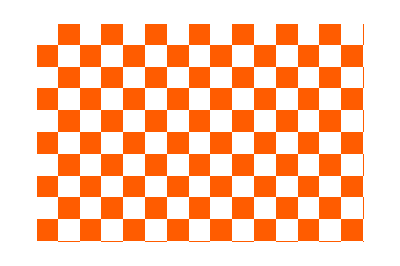

```mathematica
ArrayPlot@Table[Mod[Quotient[i,20]+Quotient[j,20],2],{i,200},{j,300}]
```

```mathematica
chunked=Partition[Partition[Table[Mod[Quotient[i,20]+Quotient[j,20],2],{i,200},{j,300}],10],10,10];
```

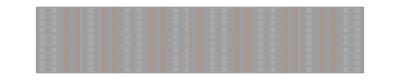
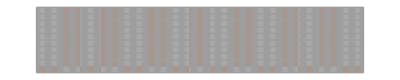
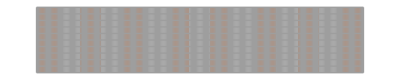
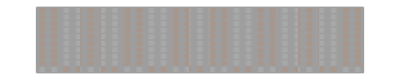
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot[#, Mesh->True]&, chunked, {2}]
```

```mathematica
blocks=Partition[Table[Mod[Quotient[i,20]+Quotient[j,20],2],{i,200},{j,300}],{20, 20}];
```

```mathematica
Map[Total[#, 2]&, blocks, {2}]
```

{{38,362,38,362,38,362,38,362,38,362,38,362,38,362,38},{362,38,362,38,362,38,362,38,362,38,362,38,362,38,362},{38,362,38,362,38,362,38,362,38,362,38,362,38,362,38},{362,38,362,38,362,38,362,38,362,38,362,38,362,38,362},{38,362,38,362,38,362,38,362,38,362,38,362,38,362,38},{362,38,362,38,362,38,362,38,362,38,362,38,362,38,362},{38,362,38,362,38,362,38,362,38,362,38,362,38,362,38},{362,38,362,38,362,38,362,38,362,38,362,38,362,38,362},{38,362,38,362,38,362,38,362,38,362,38,362,38,362,38},{362,38,362,38,362,38,362,38,362,38,362,38,362,38,362}}

```mathematica
chunked=Partition[#, 10]&/@Partition[array,10]
```

{{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}}

```mathematica
array=ConstantArray[0,{30,30}]; (*30x30 array*)
chunked=Partition[Partition[array,10],10];
chunked[[1,1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

```mathematica
evo  = Module[
{deep = 6000,initru, nru, nfit, inits, cboard},
SeedRandom[3433113];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
cboard = Table[Mod[Quotient[i,5]+Quotient[j,5],2],{i,120},{j,200}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
ca = CellularAutomaton[nru, RandomInteger[1, 200], 119];
blocks=Partition[Table[Mod[Quotient[i,20]+Quotient[j,20],2],{i,200},{j,300}],{20, 20}];tots = Map[Total[#, 2]&, blocks, {2}];
nfit =Total[Abs[cboard - CellularAutomaton[nru, RandomInteger[1, 200], 119]], 2];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]]
```

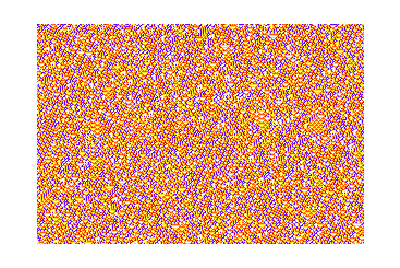

```mathematica
ArrayPlot[CellularAutomaton[{ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"], 4, 1}, RandomInteger[3, 300], 200]]
```

```mathematica
ca = CellularAutomaton[{ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"], 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];tots = Map[Total[#, 2]&, blocks, {2}];
```

```mathematica
Dimensions[blocks]
```

{10,15,20,20}

```mathematica
tots
```

{{630,654,645,641,639,665,652,628,680,664},{669,656,629,660,668,648,658,677,622,666},{663,687,643,644,690,629,656,644,649,653},{643,647,634,649,632,641,669,665,637,650},{649,658,660,676,642,651,637,652,643,641},{649,669,638,660,653,660,618,648,644,623}}

```mathematica
Differences[tots]
```

{{39,2,-16,19,29,-17,6,49,-58,2},{-6,31,14,-16,22,-19,-2,-33,27,-13},{-20,-40,-9,5,-58,12,13,21,-12,-3},{6,11,26,27,10,10,-32,-13,6,-9},{0,11,-22,-16,11,9,-19,-4,1,-18}}

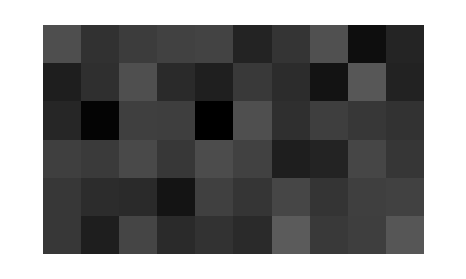

```mathematica
ArrayPlot[tots^4]
```

```mathematica
Differences[tots]
```

{{39,2,-16,19,29,-17,6,49,-58,2},{-6,31,14,-16,22,-19,-2,-33,27,-13},{-20,-40,-9,5,-58,12,13,21,-12,-3},{6,11,26,27,10,10,-32,-13,6,-9},{0,11,-22,-16,11,9,-19,-4,1,-18}}

```mathematica
Differences[#]&/@ tots
```

{{24,-9,-4,-2,26,-13,-24,52,-16},{-13,-27,31,8,-20,10,19,-55,44},{24,-44,1,46,-61,27,-12,5,4},{4,-13,15,-17,9,28,-4,-28,13},{9,2,16,-34,9,-14,15,-9,-2},{20,-31,22,-7,7,-42,30,-4,-21}}

```mathematica
{{1,2}, {3, 4}}+ {{-1, -2}, {-3, -4}}
```

{{0,0},{0,0}}

```mathematica
Dimensions[]
```

{5,10}

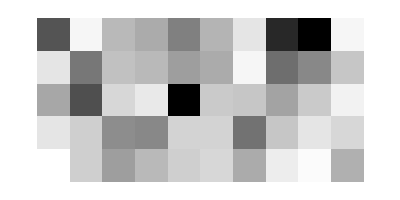

```mathematica
ArrayPlot[Abs@Differences[tots], ColorRules->Automatic]
```

```mathematica
Abs[Differences[tots]]
```

{{39,2,16,19,29,17,6,49,58,2},{6,31,14,16,22,19,2,33,27,13},{20,40,9,5,58,12,13,21,12,3},{6,11,26,27,10,10,32,13,6,9},{0,11,22,16,11,9,19,4,1,18}}

```mathematica
Length/@
```

{10,10,10,10,10}

```mathematica
Abs[Append[Differences[#], 0]&/@ tots]
```

{{24,9,4,2,26,13,24,52,16,0},{13,27,31,8,20,10,19,55,44,0},{24,44,1,46,61,27,12,5,4,0},{4,13,15,17,9,28,4,28,13,0},{9,2,16,34,9,14,15,9,2,0},{20,31,22,7,7,42,30,4,21,0}}

```mathematica
Length/@
```

{9,9,9,9,9,9}

```mathematica
Dimensions[Abs[Differences[tots]]]
```

{5,10}

```mathematica
Dimensions[Abs[Append[Differences[#], 0]&/@ tots]]
```

{6,10}

```mathematica
ca = CellularAutomaton[{ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"], 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];tots = Map[Total[#, 2]&, blocks, {2}];
```

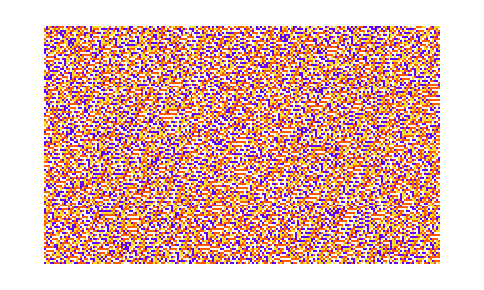

```mathematica
ArrayPlot[ca]
```

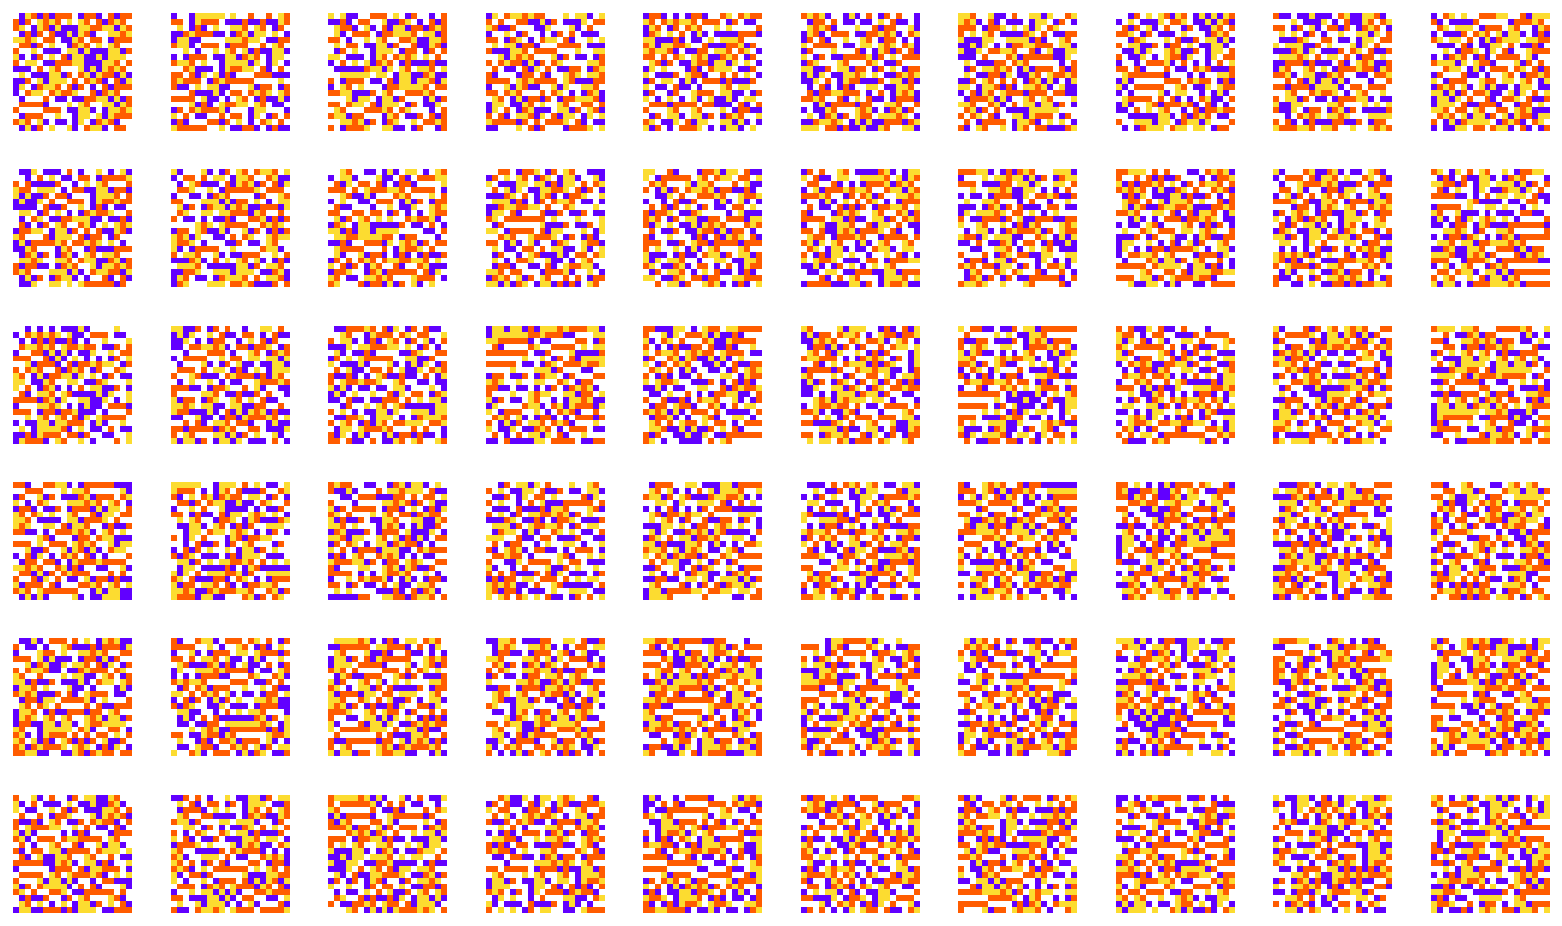

```mathematica
GraphicsGrid[Map[ArrayPlot, blocks, {2}]]
```

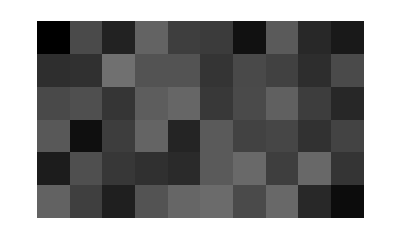

```mathematica
ArrayPlot[tots^4]
```

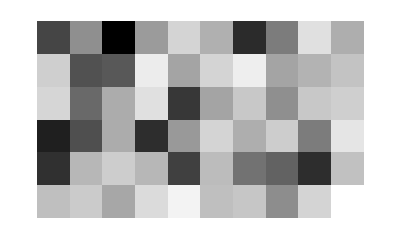

```mathematica
ArrayPlot[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], ColorRules->Automatic]
```

```mathematica
Total[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], 2]
```

2419

```mathematica
ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"]
```

```mathematica
rfs = 
Module[{width = 1200, length  = 400},
ParallelMap[With[{tots = Total/@CellularAutomaton[#, RandomInteger[1, width], {{150, 400}}]}, Append[#, "fitness"->N@Abs[Mean[tots[[-50;;]]] - Mean[tots[[;;50]]]]]]&, Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 10000]]]
```

```mathematica
SeedRandom[333444];
rf2ds = ParallelMap[Module[{ca, blocks, tots},ca = CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];
tots = Map[Total[#, 2]&, blocks, {2}];
Append[#, "fitness"->Total[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], 2]]]&, Table[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True], 10000]];
```

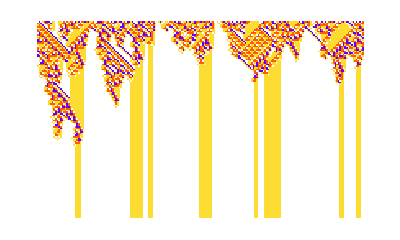
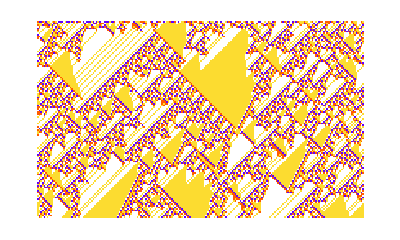
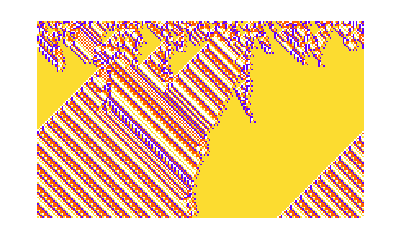
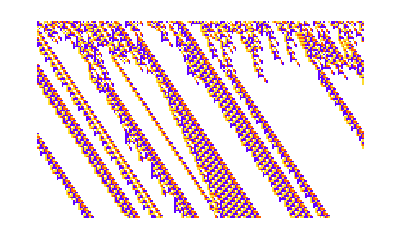
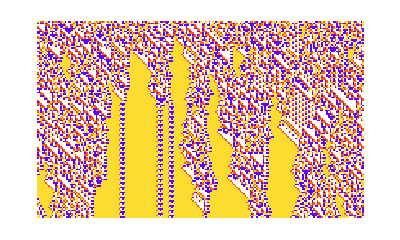
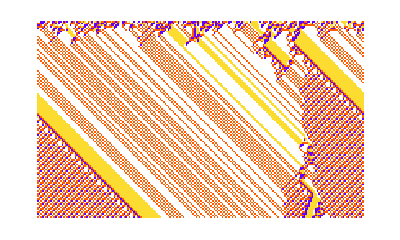
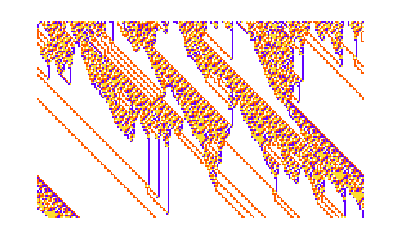
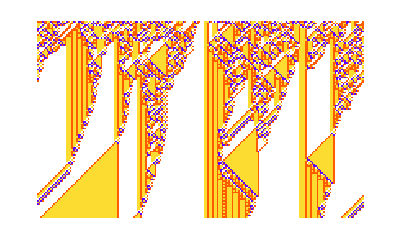

```mathematica
ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]]&/@ SortBy[rf2ds, #fitness&][[-10;;]]
```

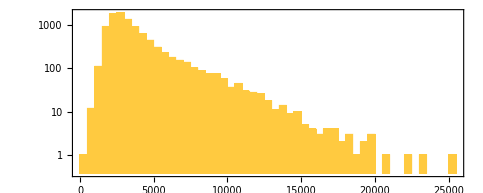

```mathematica
Histogram[#fitness&/@ rf2ds, ScalingFunctions->"Log", PlotRange->All, AspectRatio->.4,Frame->True]
```

```mathematica
Select[rf2ds, 9950<=#fitness<=10050& ]
```

{<|RuleNumber→86633462347960785967111317029965983088,Colors→4,fitness→10017|>,<|RuleNumber→6536909121034993903621896234975932720,Colors→4,fitness→10029|>,<|RuleNumber→295398975304312515093929529232555312992,Colors→4,fitness→10031|>,<|RuleNumber→324720022786600659478682684779484732684,Colors→4,fitness→9984|>,<|RuleNumber→161644222659302663399413758825187512492,Colors→4,fitness→10018|>,<|RuleNumber→56407361200670143785302841076642418720,Colors→4,fitness→9950|>,<|RuleNumber→152422895809174354946935660970675168516,Colors→4,fitness→10050|>,<|RuleNumber→81914642672998288459728666160733010732,Colors→4,fitness→9980|>}

```mathematica
GatherBy[rf2ds, #fitness&][[All, 1]]
```

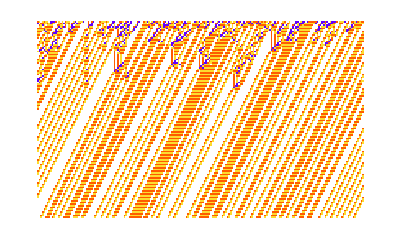
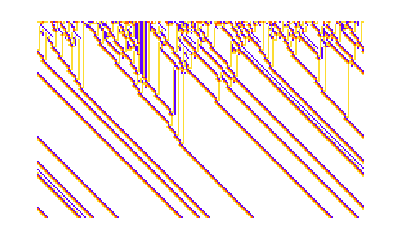
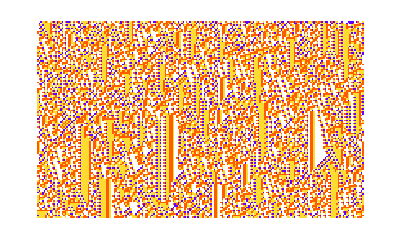
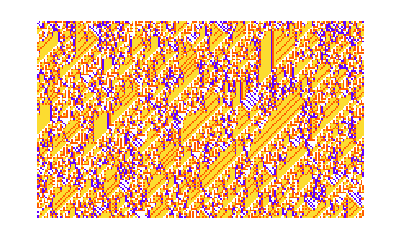
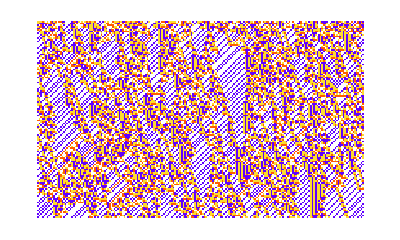
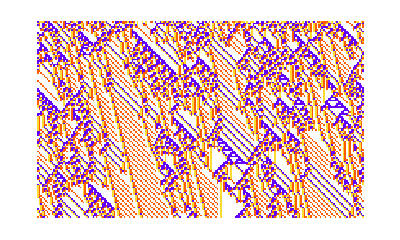
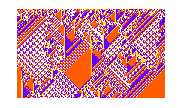
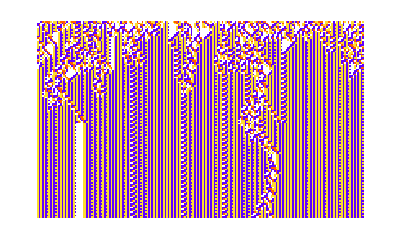

```mathematica
ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]]&/@ Select[rf2ds, 9950<=#fitness<=10050& ]
```

```mathematica
ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]]&/@ GatherBy[rf2ds, #fitness&][[All, 1]]
```

$Aborted

```mathematica
Length[GatherBy[rf2ds, #fitness&][[All, 1]]]
```

4509

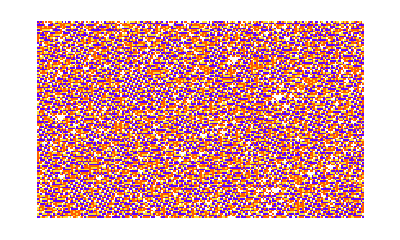
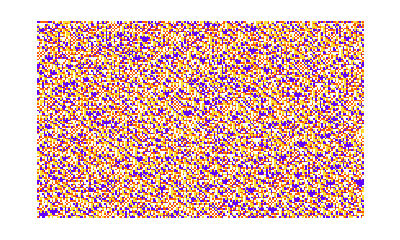
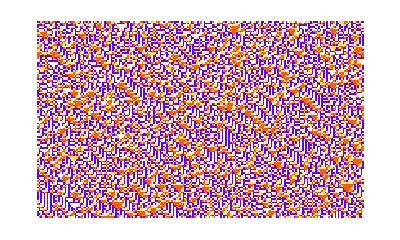
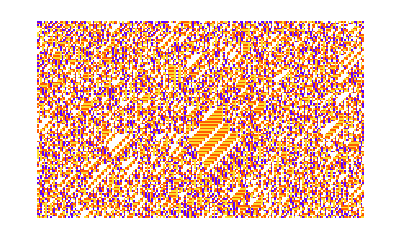
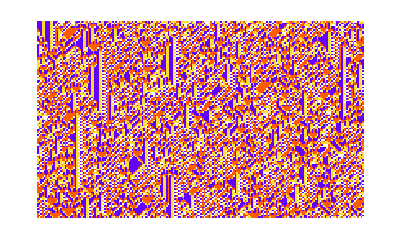
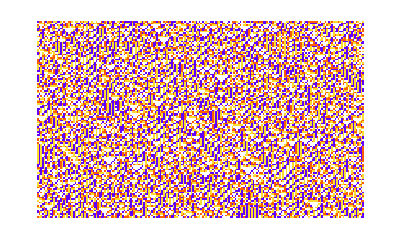
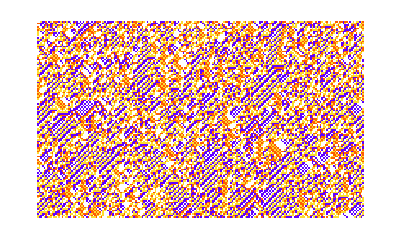
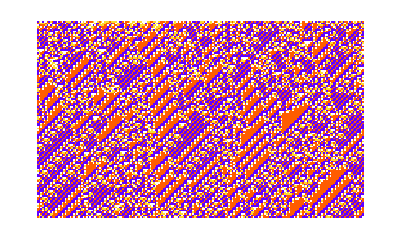
{-Graphics-2651,-Graphics-3139,-Graphics-2211,-Graphics-4241,-Graphics-4969,-Graphics-4572,-Graphics-4109,-Graphics-3351,-Graphics-3516,-Graphics-3062,-Graphics-11815,-Graphics-1849,-Graphics-2298,-Graphics-3809,-Graphics-3108,-Graphics-2099,-Graphics-3352,-Graphics-3190,-Graphics-1914,-Graphics-5507}

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]], Text[#fitness]]&/@ RandomSample[rf2ds, 20]
```

```mathematica
Length/@GatherBy[SortBy[rf2ds, #fitness&], Round[#fitness, 500]&]
```

{3,32,420,1447,2086,1652,1161,758,534,378,292,198,165,129,146,81,84,74,67,50,41,37,30,25,24,12,14,10,10,8,4,4,4,4,1,3,2,3,1,2,1,1,1,1}

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]], Text[#fitness]]&/@GatherBy[SortBy[rf2ds, #fitness&], Round[#fitness, 500]&][[All, 1]]
```

{-Graphics-309,-Graphics-752,-Graphics-1258,-Graphics-1750,-Graphics-2251,-Graphics-2750,-Graphics-3251,-Graphics-3750,-Graphics-4251,-Graphics-4750,-Graphics-5253,-Graphics-5750,-Graphics-6253,-Graphics-6756,-Graphics-7252,-Graphics-7759,-Graphics-8255,-Graphics-8761,-Graphics-9251,-Graphics-9750,-Graphics-10265,-Graphics-10752,-Graphics-11257,-Graphics-11772,-Graphics-12254,-Graphics-12769,-Graphics-13255,-Graphics-13844,-Graphics-14292,-Graphics-14808,-Graphics-15252,-Graphics-15756,-Graphics-16494,-Graphics-16763,-Graphics-17494,-Graphics-17853,-Graphics-18341,-Graphics-18963,-Graphics-19623,-Graphics-19759,-Graphics-20765,-Graphics-22469,-Graphics-23237,-Graphics-25418}

```mathematica
ArrayPlot[CellularAutomaton[{110,2, 1}, RandomInteger[1, 200], 120]]
```

-Graphics-

### Testing on symmetric rules

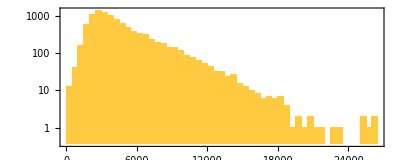

```mathematica
Histogram[#fitness&/@ rf2dss, ScalingFunctions->"Log", PlotRange->All, AspectRatio->.4,Frame->True]
```

```mathematica
SeedRandom[333444];
rf2dss = ParallelMap[Module[{ca, blocks, tots},ca = CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];
tots = Map[Total[#, 2]&, blocks, {2}];
Append[#, "fitness"->Total[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], 2]]]&, Table[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"], 10000]];
```

```mathematica
SeedRandom[222222];Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]], Text[#fitness]]&/@GatherBy[SortBy[rf2dss, #fitness&], Round[#fitness, 500]&][[All, 1]]
```

{-Graphics-84,-Graphics-272,-Graphics-758,-Graphics-1251,-Graphics-1751,-Graphics-2251,-Graphics-2750,-Graphics-3251,-Graphics-3752,-Graphics-4251,-Graphics-4750,-Graphics-5255,-Graphics-5750,-Graphics-6251,-Graphics-6752,-Graphics-7252,-Graphics-7751,-Graphics-8255,-Graphics-8753,-Graphics-9257,-Graphics-9755,-Graphics-10253,-Graphics-10766,-Graphics-11255,-Graphics-11753,-Graphics-12302,-Graphics-12751,-Graphics-13255,-Graphics-13761,-Graphics-14269,-Graphics-14756,-Graphics-15324,-Graphics-15750,-Graphics-16260,-Graphics-16937,-Graphics-17254,-Graphics-17818,-Graphics-18348,-Graphics-18836,-Graphics-19915,-Graphics-20885,-Graphics-21274,-Graphics-21871,-Graphics-22881,-Graphics-23467,-Graphics-25061,-Graphics-25467,-Graphics-26151}

```mathematica
Select[rf2dss, #fitness == 15750&]
```

{<|RuleNumber→126931591398812896288913507267985322316,Colors→4,fitness→15750|>}

```mathematica
ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 3000], 2000]]&[Select[rf2dss2, #fitness == 18453&][[1]]]
```

-Graphics-

```mathematica
SeedRandom[333445];
rf2dss2 = ParallelMap[Module[{ca, blocks, tots},ca = CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];
tots = Map[Total[#, 2]&, blocks, {2}];
Append[#, "fitness"->Total[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], 2]]]&, Table[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"], 10000]];
```

```mathematica
SeedRandom[222222];Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119]], Text[#fitness]]&/@GatherBy[SortBy[rf2dss2, #fitness&], Round[#fitness, 500]&][[All, 1]]
```

{-Graphics-151,-Graphics-290,-Graphics-777,-Graphics-1263,-Graphics-1750,-Graphics-2251,-Graphics-2750,-Graphics-3251,-Graphics-3750,-Graphics-4252,-Graphics-4750,-Graphics-5251,-Graphics-5750,-Graphics-6253,-Graphics-6754,-Graphics-7251,-Graphics-7751,-Graphics-8252,-Graphics-8752,-Graphics-9255,-Graphics-9757,-Graphics-10254,-Graphics-10773,-Graphics-11267,-Graphics-11763,-Graphics-12254,-Graphics-12753,-Graphics-13251,-Graphics-13767,-Graphics-14274,-Graphics-14766,-Graphics-15321,-Graphics-15817,-Graphics-16443,-Graphics-16789,-Graphics-17317,-Graphics-17769,-Graphics-18453,-Graphics-18985,-Graphics-19423,-Graphics-19811,-Graphics-20275,-Graphics-22000,-Graphics-22317,-Graphics-23466,-Graphics-24096,-Graphics-24765,-Graphics-27336,-Graphics-31350}

### Trying 1 / pi with more colors

```mathematica
Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432113 + i];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Abs[( 1 / Pi )- Count[CellularAutomaton[nru, RandomInteger[1, 200], {{{120}}}], 1]/200];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]]
```

### Studying nice rules

```mathematica
Length[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"]]
```

14778

```mathematica
{{"[◼]", "$LifetimeData"}}[2, 2]
```

[◼] | $LifetimeData [2,2]

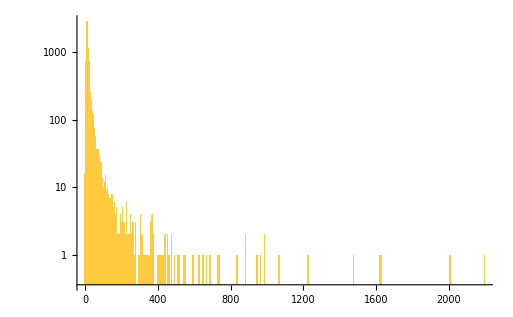

```mathematica
Histogram[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"],  ScalingFunctions->"Log", PlotRange->All]
```

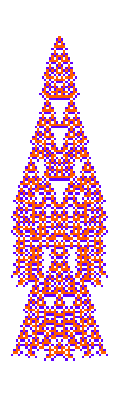
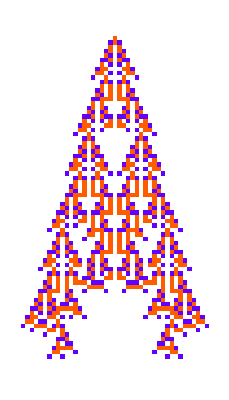
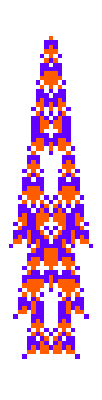
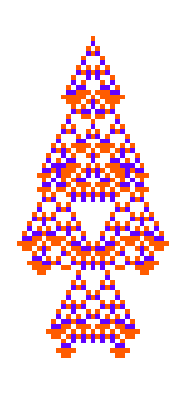
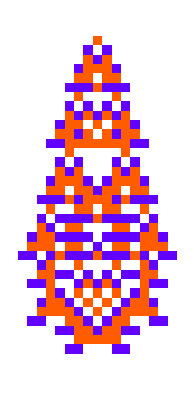
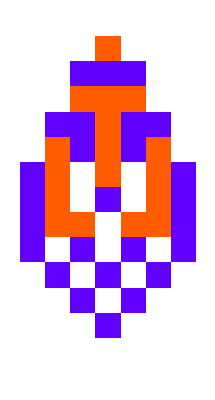
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ca = CellularAutomaton[{#[[1]], 3, 1}, {{1}, 0}, 1000], lt},
lt =  {{"[◼]", "TestCALifeTime"}}[ca];ArrayPlot[ca[[;;If[lt == -Infinity, 1000, lt + 1]]], ImageSize->10Sqrt[lt]]]&/@Keys[ReverseSort[RandomSample[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 100]]]
```

```mathematica
KeyValueMap[Module[{ca = CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100], lt},
lt =  {{"[◼]", "TestCALifeTime"}}[ca];Labeled[ArrayPlot[ca[[;;100]]], Text[#2]]]&,ReverseSort[RandomSample[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 100]]]
```

{-Graphics-162,-Graphics-97,-Graphics-72,-Graphics-67,-Graphics-59,-Graphics-59,-Graphics-54,-Graphics-53,-Graphics-50,-Graphics-45,-Graphics-42,-Graphics-40,-Graphics-39,-Graphics-38,-Graphics-37,-Graphics-35,-Graphics-31,-Graphics-30,-Graphics-28,-Graphics-27,-Graphics-27,-Graphics-26,-Graphics-26,-Graphics-24,-Graphics-24,-Graphics-24,-Graphics-23,-Graphics-23,-Graphics-23,-Graphics-22,-Graphics-22,-Graphics-22,-Graphics-21,-Graphics-21,-Graphics-21,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-18,-Graphics-18,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-16,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-10,-Graphics-10,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-8,-Graphics-8,-Graphics-8,-Graphics-8,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-6,-Graphics-6,-Graphics-5,-Graphics-5,-Graphics-4}

```mathematica
Module[
{goal=50,deep=5000,cut=200,ru,life,evo,res},
SeedRandom[23563];
res=ParallelTable[
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],1],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal
]<=Abs[Last[#]-goal],{ru,life},#]
]&,{{0,3,1},0},deep];evo,100];
ListStepPlot[(Last/@#)&/@res,
Frame->True,AspectRatio->1/3]
]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
rh = Reap[mh = Module[{ru,ca,lt,lts, pcas,fitness, initru = {0,4,1}, initfit = {0}},SeedRandom[7899623];
Sow[{initru,<||>, initfit}];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca=CellularAutomaton[ru,{{1},0},{200,{-200,200}}];
lt={{"[◼]", "TestCALifeTime"}}[ca];
If[lt==-Infinity,Sow[{ru, <||>,{lt}}];#,
pcas=Table[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-200,200}},1],Ceiling[lt/10]];
fitness=Min[lts = Join[{lt},{{"[◼]", "TestCALifeTime"}}/@(First/@pcas)]];
Sow[{ru, Last/@pcas,lts}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{initru, First[initfit]},2000]]][[2, 1]];
```

```mathematica
Row[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,25 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last]),Spacer[1]]
```

### Fr